```mathematica
(* PRÁCTICA 2 *)
```

```mathematica
(* SESIÓN 1 *)
(* Implementado por: - Lishuang Sun - Fabián Scherle Carboneres *)
(*Ejercicio 1*)
```

```mathematica
ReglaBinario[Regla_Integer]:=Module[{i,num,aux,modulo},
(* La regla en decimal *)
aux=Regla;
(* Números decimales de 0 a 7 en binario *)
num={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};

For[i=1,i≤ 8,i++,
(* Convertir la regla en formato binario, el reverso *)
modulo=Mod[aux,2];
aux=Quotient[aux,2];
(* Añade cada 0 o 1 de la regla en la lista i *)
AppendTo[num[[i]],modulo];
];
Return[num];
]
```

```mathematica
ReglaBinario[54]
```

{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}}

```mathematica
Transicion[regla_List, config_List] := Module[{i,len,neighbourL,neighbourR,sigEstado,newConfig},
newConfig={};
len=Length[config];
(* Recorrido de todas las células *)
For[i=1, i≤len, i++,
(* Cálculo de los vecinos izquierdo y derecho de la célula *)
If[i==1,neighbourL=config[[len]];,neighbourL=config[[i-1]];];
If[i==len,neighbourR=config[[1]];,neighbourR=config[[i+1]];];
(* Hace matching para saber a qué configuración de célula transitar *)
sigEstado=Cases[regla,{neighbourL,config[[i]],neighbourR,_}];
(* Añade a la solución el nuevo estado de la célula *)
AppendTo[newConfig,sigEstado[[1,4]]];
];
Return [newConfig];
]
```

```mathematica
(* Usando la regla 54 *)
Transicion[{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}},{1,0,1,0,1,0,1,0,1}]
```

{0,1,1,1,1,1,1,1,0}

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{i,aux,final,reg},
(* Partimos de la configuración inicial *)
aux=Inicial;final={Inicial};
(* Expresamos la regla adecuadamente *)
reg=ReglaBinario[Regla];

(* Calcular t configuraciones *)
For[i=0,i<t,i++,
aux=Transicion[reg,aux];
AppendTo[final,aux];
];
(* Visualización de las t+1 configuraciones *)
ArrayPlot[final]
]
```

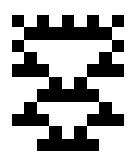

```mathematica
AC[{1,0,1,0,1,0,1,0,1},54,10]
```

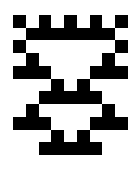

```mathematica
(* Comprobación con funciones de Mathematica *)
ArrayPlot[CellularAutomaton[54,{1,0,1,0,1,0,1,0,1},10]]
```

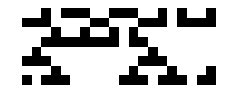

```mathematica
(* Usando la regla 22 *)
AC[{0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1},22,7]
```